# Positivity stuffs

## Gluon coefficient function

#### Bare part

```mathematica
cgbarex[z_]:=-8z^2 + 8z-1
```

```mathematica
cgbareNp[n_]=Integrate[z^(n-1)*cgbarex[z], {z,0,1}, Assumptions->Re[n]>0]
cgbareN[n_]:=(-8/(n+2)+8/(n+1)-1/n)
```

-1/n+8/(2+3 n+n^2)

```mathematica
FullSimplify[cgbareNp@n- cgbareN@n]
```

0

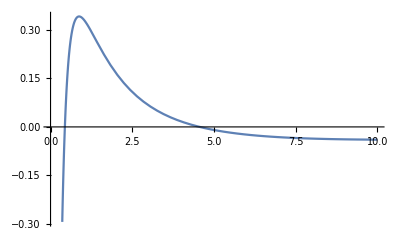

```mathematica
Plot[cgbareN@n, {n, 0, 10}]
```

#### Subtraction part

```mathematica
cgsubx[z_] := ((1-z)^2 + z^2)Log[(1-z)/z]
```

```mathematica
cgsubN[n_] = Integrate[z^(n-1)*cgsubx[z], {z,0,1}, Assumptions->Re[n]>0]
```

(2 HarmonicNumber[n])/(1+n)-(2 HarmonicNumber[1+n])/(2+n)-(EulerGamma+PolyGamma[0,n])/n

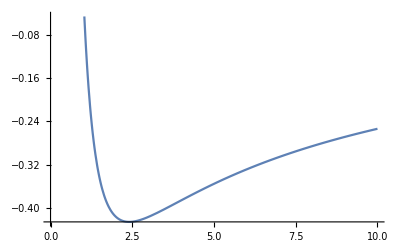

```mathematica
Plot [cgsubN@n, {n,0,10}]
```

#### Compare to Vogt et al.

```mathematica
s1[n_] =  Sum[1/k, {k,1,n}]
s2[n_] = Sum[1/k^2, {k,1,n}]
s1c1[n_] = Sum[s1@k/k, {k,1,n}]
```

HarmonicNumber[n]

HarmonicNumber[n,2]

1/2 (HarmonicNumber[n]^2+HarmonicNumber[n,2])

```mathematica
gqg[f_, n_] := 2f[n+2] - 4f[n+1] - f[n-1] + 3f[n]
```

We are using the coefficient function without the proper normalization, provided that it is irrelevant in comparisons

```mathematica
vogtcg [n_] = -2 (gqg[s1c1 , n] + 4gqg[s1,n]-gqg[s2,n]) -6(s1[n-1] - s1[n])
```

-6 (HarmonicNumber[-1+n]-HarmonicNumber[n])-2 (HarmonicNumber[2+n]^2+4 (-HarmonicNumber[-1+n]+3 HarmonicNumber[n]-4 HarmonicNumber[1+n]+2 HarmonicNumber[2+n])+1/2 (-HarmonicNumber[-1+n]^2-HarmonicNumber[-1+n,2])+HarmonicNumber[-1+n,2]-3 HarmonicNumber[n,2]+3/2 (HarmonicNumber[n]^2+HarmonicNumber[n,2])+4 HarmonicNumber[1+n,2]-2 (HarmonicNumber[1+n]^2+HarmonicNumber[1+n,2])-HarmonicNumber[2+n,2])

```mathematica
FullSimplify[1/2vogtcg[n] - cgbareN[n]-cgsubN[n]]
```

0

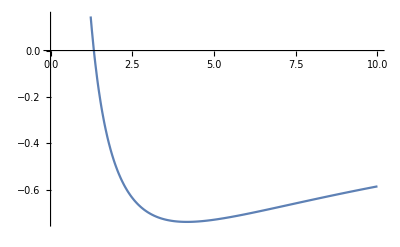

```mathematica
Plot[vogtcg@n, {n,0,10}]
```

## Quark coefficient function

#### Bare part

```mathematica
cqbareN[n_] = Integrate[(6+4z)z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0]-(9+4Zeta[2])
```

-9+(6+10 n)/(n+n^2)-(2 π^2)/3

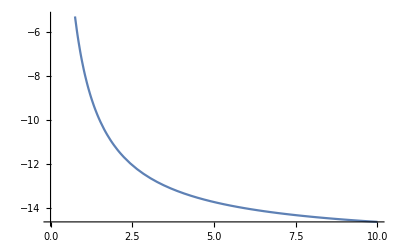

```mathematica
Plot [cqbareN@n, {n,0,10}]
```

#### Subtraction part

```mathematica
cqsubN[n_] = Integrate[(4Log[1-z]/(1-z) -3/(1-z))(z^(n-1)-1) +(-2(1+z)Log[(1-z)/z] - 4 Log[z]/(1-z))z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0]
```

1/(3 n^2 (1+n))(6+n (12+3 EulerGamma (2+n (7+3 n+2 EulerGamma (1+n)))+n (1+n) π^2)+3 n ((2+n (7+3 n+4 EulerGamma (1+n))) PolyGamma[0,n]+2 n (1+n) PolyGamma[0,n]^2+2 n (1+n) PolyGamma[1,1+n]))

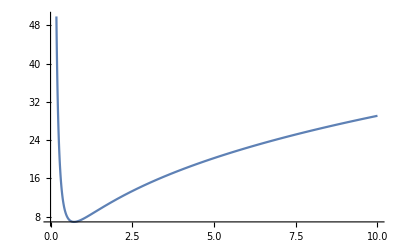

```mathematica
Plot [cqsubN@n, {n,0,10}]
```

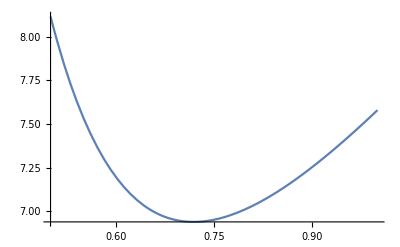

```mathematica
Plot[cqsubN@n, {n,0.5,1}]
```

#### Compare to Vogt et al.

```mathematica
gqq[f_, n_] := f[n+1] + f[n-1]
```

We are using the coefficient function without the proper normalization, provided that it is irrelevant in comparisons

```mathematica
vogtcq[n_] := 9(s1@n-1) +2(gqq[s1c1,n]+2gqq[s1,n]-gqq[s2,n])-7(s1[n-1]+s1[n])
```

```mathematica
FullSimplify[vogtcq[n]-cqbareN[n]-cqsubN[n]]
```

0

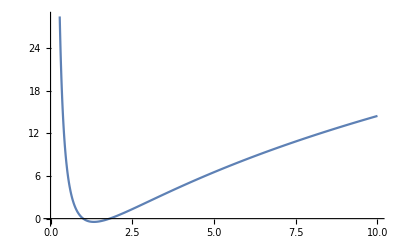

```mathematica
Plot[vogtcq@n, {n,0,10}]
```